## NDRoot usage

### basic usage

```mathematica
Quit[]
```

```mathematica
Needs@"NDRoot`"
```

Define a complicated numeric function

```mathematica
f[
x_?NumericQ,
y_?NumericQ,
z_?NumericQ
]:=-(y BesselY[1,x]+BesselY[0,x])BesselJ[0,x z]+(y BesselJ[1,x]+BesselJ[0,x])BesselY[0,x z]
```

This has one root near x=10^-10

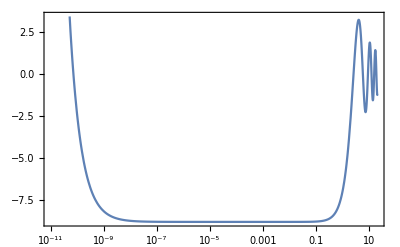

```mathematica
fPlot=LogLinearPlot[
f[x,10^-9,10^-6],
{x,10^-11,20},
Axes->{True,False},
AxesOrigin->{0,0},
Frame->True
]
```

and a series of nearly equally spaced roots starting around x=π:

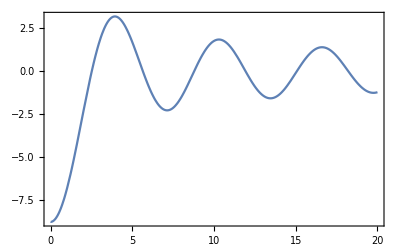

```mathematica
Plot[
f[x,10^-9,10^-6],
{x,0,20},
Axes->{True,False},
AxesOrigin->{0,0},
Frame->True
]
```

NDRoot can find all these roots:

```mathematica
fRoots=NDRoot[f[x,10^-9,10^-6],{x,10^-11,20}]
```

{x[1]→7.23824×10^-11,x[2]→2.52297,x[3]→5.64764,x[4]→8.78632,x[5]→11.9277,x[6]→15.07,x[7]→18.2125}

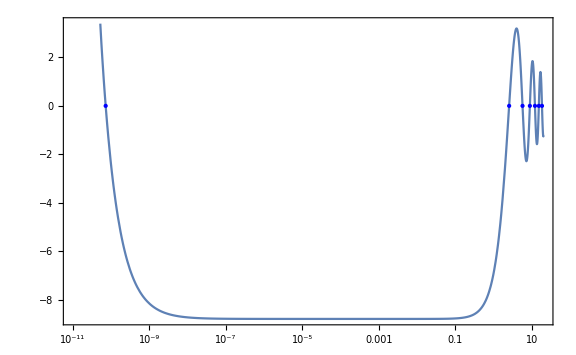

```mathematica
Show[
fPlot,
Epilog->{
Blue,
PointSize@Medium,
Point@Thread[{Log[Values@fRoots],0}]
},
ImageSize->Large
]
```

### advanced usage

#### step size

Consider a function with many closely spaced roots:

```mathematica
g[x_?NumericQ,y_?NumericQ]:=BesselJ[1.1,x y]BesselY[0.1,x]-BesselJ[0.1,x]BesselY[1.1,x y]
```

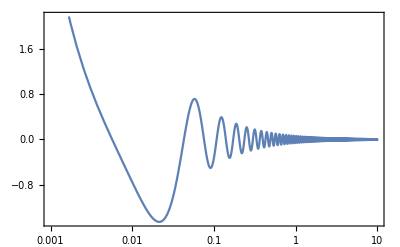

```mathematica
gPlot=LogLinearPlot[
g[x,10^2],
{x,10^-3,10},
Axes->{True,False},
AxesOrigin->{0,0},
Frame->True,
MaxRecursion->10
]
```

NDRoot will find some of the roots in an interval:

```mathematica
NDRoot[g[x,10^2],{x,10^-2,10}]
```

{x[1]→0.744478,x[2]→1.09385,x[3]→3.3475,x[4]→5.6007,x[5]→7.79035,x[6]→9.85305}

Set the step size appropriately to capture all the roots in the interval:

```mathematica
gRoots=NDRoot[g[x,10^2],{x,10^-3,10},MaxStepSize->0.001]
```

{x[1]→0.00567691,x[2]→0.0428303,x[3]→0.0754731,x[4]→0.107697,x[5]→0.139764,x[6]→0.171749,x[7]→0.203684,x[8]→0.235584,x[9]→0.26746,x[10]→0.299318,x[11]→0.33116,x[12]→0.36299,x[13]→0.394811,x[14]→0.426623,x[15]→0.458429,x[16]→0.490228,x[17]→0.522022,x[18]→0.553812,x[19]→0.585597,x[20]→0.617379,x[21]→0.649158,x[22]→0.680934,x[23]→0.712707,x[24]→0.744478,x[25]→0.776246,x[26]→0.808013,x[27]→0.839778,x[28]→0.871541,x[29]→0.903303,x[30]→0.935064,x[31]→0.966823,x[32]→0.998581,x[33]→1.03034,x[34]→1.06209,x[35]→1.09385,x[36]→1.1256,x[37]→1.15735,x[38]→1.18911,x[39]→1.22086,x[40]→1.25261,x[41]→1.28436,x[42]→1.31611,x[43]→1.34786,x[44]→1.37961,x[45]→1.41135,x[46]→1.4431,x[47]→1.47485,x[48]→1.50659,x[49]→1.53834,x[50]→1.57008,x[51]→1.60183,x[52]→1.63357,x[53]→1.66532,x[54]→1.69706,x[55]→1.72881,x[56]→1.76055,x[57]→1.79229,x[58]→1.82404,x[59]→1.85578,x[60]→1.88752,x[61]→1.91926,x[62]→1.951,x[63]→1.98275,x[64]→2.01449,x[65]→2.04623,x[66]→2.07797,x[67]→2.10971,x[68]→2.14145,x[69]→2.17319,x[70]→2.20493,x[71]→2.23667,x[72]→2.26841,x[73]→2.30015,x[74]→2.33189,x[75]→2.36363,x[76]→2.39537,x[77]→2.42711,x[78]→2.45885,x[79]→2.49058,x[80]→2.52232,x[81]→2.55406,x[82]→2.5858,x[83]→2.61754,x[84]→2.64928,x[85]→2.68101,x[86]→2.71275,x[87]→2.74449,x[88]→2.77623,x[89]→2.80797,x[90]→2.8397,x[91]→2.87144,x[92]→2.90318,x[93]→2.93492,x[94]→2.96665,x[95]→2.99839,x[96]→3.03013,x[97]→3.06187,x[98]→3.0936,x[99]→3.12534,x[100]→3.15708,x[101]→3.18881,x[102]→3.22055,x[103]→3.25229,x[104]→3.28402,x[105]→3.31576,x[106]→3.3475,x[107]→3.37923,x[108]→3.41097,x[109]→3.44271,x[110]→3.47444,x[111]→3.50618,x[112]→3.53791,x[113]→3.56965,x[114]→3.60139,x[115]→3.63312,x[116]→3.66486,x[117]→3.69659,x[118]→3.72833,x[119]→3.76007,x[120]→3.7918,x[121]→3.82354,x[122]→3.85527,x[123]→3.88701,x[124]→3.91874,x[125]→3.95048,x[126]→3.98222,x[127]→4.01395,x[128]→4.04569,x[129]→4.07742,x[130]→4.10916,x[131]→4.14089,x[132]→4.17263,x[133]→4.20436,x[134]→4.2361,x[135]→4.26784,x[136]→4.29957,x[137]→4.33131,x[138]→4.36304,x[139]→4.39478,x[140]→4.42651,x[141]→4.45825,x[142]→4.48998,x[143]→4.52172,x[144]→4.55345,x[145]→4.58519,x[146]→4.61692,x[147]→4.64866,x[148]→4.68039,x[149]→4.71213,x[150]→4.74386,x[151]→4.7756,x[152]→4.80733,x[153]→4.83907,x[154]→4.8708,x[155]→4.90254,x[156]→4.93427,x[157]→4.96601,x[158]→4.99774,x[159]→5.02948,x[160]→5.06121,x[161]→5.09294,x[162]→5.12468,x[163]→5.15641,x[164]→5.18815,x[165]→5.21988,x[166]→5.25162,x[167]→5.28335,x[168]→5.31509,x[169]→5.34682,x[170]→5.37856,x[171]→5.41029,x[172]→5.44203,x[173]→5.47376,x[174]→5.50549,x[175]→5.53723,x[176]→5.56896,x[177]→5.6007,x[178]→5.63243,x[179]→5.66417,x[180]→5.6959,x[181]→5.72764,x[182]→5.75937,x[183]→5.79111,x[184]→5.82284,x[185]→5.85457,x[186]→5.88631,x[187]→5.91804,x[188]→5.94978,x[189]→5.98151,x[190]→6.01325,x[191]→6.04498,x[192]→6.07671,x[193]→6.10845,x[194]→6.14018,x[195]→6.17192,x[196]→6.20365,x[197]→6.23539,x[198]→6.26712,x[199]→6.29885,x[200]→6.33059,x[201]→6.36232,x[202]→6.39406,x[203]→6.42579,x[204]→6.45753,x[205]→6.48926,x[206]→6.52099,x[207]→6.55273,x[208]→6.58446,x[209]→6.6162,x[210]→6.64793,x[211]→6.67966,x[212]→6.7114,x[213]→6.74313,x[214]→6.77487,x[215]→6.8066,x[216]→6.83833,x[217]→6.87007,x[218]→6.9018,x[219]→6.93354,x[220]→6.96527,x[221]→6.99701,x[222]→7.02874,x[223]→7.06047,x[224]→7.09221,x[225]→7.12394,x[226]→7.15568,x[227]→7.18741,x[228]→7.21914,x[229]→7.25088,x[230]→7.28261,x[231]→7.31435,x[232]→7.34608,x[233]→7.37781,x[234]→7.40955,x[235]→7.44128,x[236]→7.47302,x[237]→7.50475,x[238]→7.53648,x[239]→7.56822,x[240]→7.59995,x[241]→7.63168,x[242]→7.66342,x[243]→7.69515,x[244]→7.72689,x[245]→7.75862,x[246]→7.79035,x[247]→7.82209,x[248]→7.85382,x[249]→7.88556,x[250]→7.91729,x[251]→7.94902,x[252]→7.98076,x[253]→8.01249,x[254]→8.04423,x[255]→8.07596,x[256]→8.10769,x[257]→8.13943,x[258]→8.17116,x[259]→8.20289,x[260]→8.23463,x[261]→8.26636,x[262]→8.2981,x[263]→8.32983,x[264]→8.36156,x[265]→8.3933,x[266]→8.42503,x[267]→8.45677,x[268]→8.4885,x[269]→8.52023,x[270]→8.55197,x[271]→8.5837,x[272]→8.61543,x[273]→8.64717,x[274]→8.6789,x[275]→8.71064,x[276]→8.74237,x[277]→8.7741,x[278]→8.80584,x[279]→8.83757,x[280]→8.8693,x[281]→8.90104,x[282]→8.93277,x[283]→8.96451,x[284]→8.99624,x[285]→9.02797,x[286]→9.05971,x[287]→9.09144,x[288]→9.12317,x[289]→9.15491,x[290]→9.18664,x[291]→9.21838,x[292]→9.25011,x[293]→9.28184,x[294]→9.31358,x[295]→9.34531,x[296]→9.37704,x[297]→9.40878,x[298]→9.44051,x[299]→9.47225,x[300]→9.50398,x[301]→9.53571,x[302]→9.56745,x[303]→9.59918,x[304]→9.63091,x[305]→9.66265,x[306]→9.69438,x[307]→9.72611,x[308]→9.75785,x[309]→9.78958,x[310]→9.82132,x[311]→9.85305,x[312]→9.88478,x[313]→9.91652,x[314]→9.94825,x[315]→9.97998}

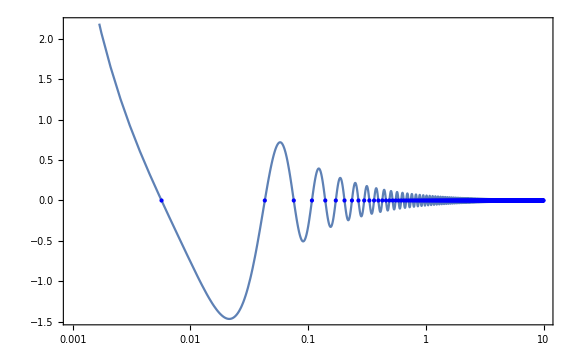

```mathematica
Show[
gPlot,
Epilog->{
Blue,
PointSize@Medium,
Point@Thread[{Log[Values@gRoots],0}]
},
ImageSize->Large
]
```

#### specific roots

To find the (up to) 10 roots closest to a point, we use

```mathematica
NDRoot[g[x,10^2],{x,0.3,10^-2,10},10,MaxStepSize->0.001]
```

{x[1]→0.299318,x[2]→0.33116,x[3]→0.26746,x[4]→0.36299,x[5]→0.235584,x[6]→0.394811,x[7]→0.203684,x[8]→0.426623,x[9]→0.171749,x[10]→0.458429}

or

```mathematica
NDRoot[g[x,10^2],{x,0.3},10,Direction->"TwoSided",MaxStepSize->0.001]
```

{x[1]→0.299318,x[2]→0.33116,x[3]→0.26746,x[4]→0.36299,x[5]→0.235584,x[6]→0.394811,x[7]→0.203684,x[8]→0.426623,x[9]→0.171749,x[10]→0.458429}

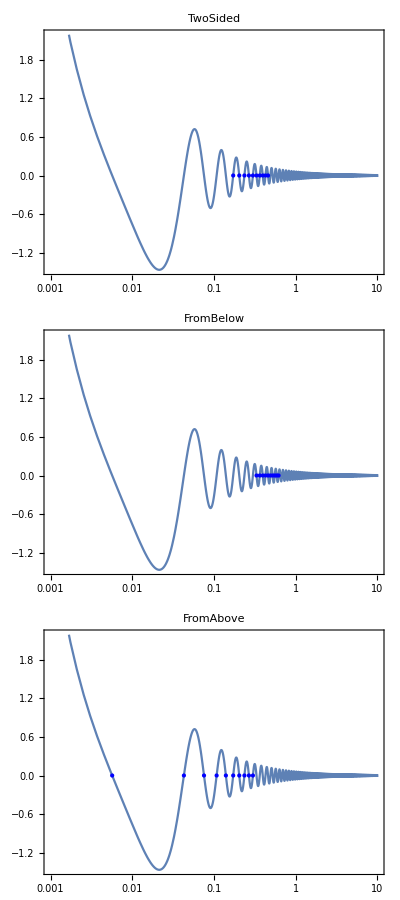

```mathematica
Table[
With[
{
roots=NDRoot[g[x,10^2],{x,0.3},10,Direction->dir,MaxStepSize->0.001]
},

Show[
gPlot,
PlotLabel->dir,
Axes->True,
AxesOrigin->{Log@0.3,0},
ImageSize->Medium,
Epilog->{
Blue,
PointSize@Medium,
Point@Thread[{Log[Values@roots],0}]
}
]

],

{dir,{"TwoSided","FromBelow","FromAbove"}}
]//Column
```

To find the 10^th closest root, we use

```mathematica
NDRoot[g[x,10^2],{x,0.3,10^-2,10},{10},MaxStepSize->0.001]
```

0.458429

or

```mathematica
NDRoot[g[x,10^2],{x,0.3},{10},Direction->"FromBelow",MaxStepSize->0.001]
```

0.617379

```mathematica
NDRoot[g[x,10^2],{x,0.3},{10},Direction->"FromAbove",MaxStepSize->0.001]
```

0.00567691